```mathematica
Fglobal[gr_,pos_]:=2.^(0.95*(1.1-gr))*2.^(1-(0.78+0.15/gr)*pos/(0.69/gr));
rnadeg=8.3;
trsini=400;
trsinr=200;
trslrr=200;
kdeg=0.8;
kgsini=0.6;
kgslrr=0.6;
dgsini=5;
dgslrr=1;
kb1=0.32;
kb2=0.32;
kd1=0.032;
kd2=0.032;
kud1=39.7;
kud2=214.1;
vsini0=0;
vsini1=25;
vsinr=40;
vslrr0=80.2;
vslrr1=0;
Spo0Apd=1.5;
vt=30;
trtap=100;

SinItot:=(Spo0Apd/(Spo0Apd+5)*vsini1)/rnadeg*trsini/(0.2+gr)*Fglobal[gr,0.8];
SinRtot:=vsinr/rnadeg*trsinr/(0.2+gr)*Fglobal[gr,0.8];
SinISinR[SinId_,SinRd_]:=2*kb1*SinId*SinRd/(gr+0.2);
krslrr[SinRt_]:=(SinRt/(SinRt+5)); (*kgslrr:the fraction of sinr-occupied slrr promoter, SinRt: sinR tetramer*)
SlrRtot[SinRt_]:=(vslrr1*krslrr[SinRt]+vslrr0(1-krslrr[SinRt]))/rnadeg*trslrr/(gr+kdeg)*Fglobal[gr,0.3];
SlrRSinR[SlrRd_,SinRd_]:=kb2*SlrRd*SinRd/(gr+0.2+1.1661);
dSinId[SinId_,SinRd_]:=(SinItot-SinISinR[SinId,SinRd]-SinId*2)^2*kd2-(kud2+gr+0.2)*SinId*2;
dSinRd[SinRd_,SinId_,SlrRd_]:=2*(SinRtot-SinISinR[SinId,SinRd]/2-SinRd-SlrRSinR[SlrRd,SinRd])*(kud1)-SinRd^2*kd1-SinRd*(gr+0.2);
SinRt[SinId_,SinRd_,SlrRd_]:=SinRtot-SinISinR[SinId,SinRd]/2-SinRd-SlrRSinR[SlrRd,SinRd];
gr=0.2;
Tap[R_]:=vt/rnadeg*trtap(1-R/(R+8))*Fglobal[gr,0.8];
```

```mathematica
Rds1={};Rds2={};Rds={};Rds0={};Rdst={};
For[Spo0Ap=0.0001,Spo0Ap<1,Spo0Ap=Spo0Ap+0.001;Spo0Apd:= (13+4 Spo0Ap-√13 √(13+8 *Spo0Ap))*125,sol=Solve[{dSinId[Id,Rd]==0,dSinRd[Rd,Id,Ld]==0,SlrRtot[(SinRtot-SinISinR[Id,Rd]/2-Rd-SlrRSinR[Ld,Rd])]==SlrRSinR[Ld,Rd]+Ld,Ld>0,Rd>0,Id>0},{Ld,Rd,Id},Reals,WorkingPrecision->12];
temp=Sort[Tap[SinRt[Id,Rd,Ld]]/.sol];Rdst=Append[Rdst,temp];If[temp[[1]]<50,Rds1=Append[Rds1,{Spo0Ap,temp[[1]]}]];
If[Last[temp]>50,Rds2=Append[Rds2,{Spo0Ap,Last[temp]}]];
If[temp[[1]]<50 && Last[temp]>50 && Length[temp]>2,Rds=Append[Rds,{Spo0Ap,temp[[3]]}];Rds0=Append[Rds0,{Spo0Ap,temp[[4]]}]];
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Rdst
```

{{2.17091,2.17148},{2.17265,2.17521},{2.17948,2.18448},{2.1915,2.19902},{2.20861,2.21873},{2.23066,2.24348},{2.2575,2.27313},{2.28895,2.30754},{2.32481,2.34653},{2.36487,2.38991},{2.40892,2.43747},{2.45672,2.48901},{2.50802,2.5443},{2.56259,2.6031},{2.62018,2.66518},{2.68052,2.73029},{2.74336,2.79818},{2.80845,2.86861},{2.87554,2.94133},{2.94439,3.0161,937.838,996.105},{3.01476,3.09268,917.665,1002.23},{3.08641,3.17084,900.259,1005.9},{3.15913,3.25034,884.338,1008.43},{3.23271,3.33097,869.437,1010.29},{3.30693,3.41252,855.334,1011.72},{3.38161,3.49479,841.902,1012.85},{3.45658,3.57759,829.066,1013.76},{3.53165,3.66074,816.771,1014.52},{3.60668,3.74406,804.981,1015.15},{3.68152,3.8274,793.666,1015.68},{3.75604,3.91061,782.802,944.62,954.438,1016.13},{3.83012,3.99356,772.368,917.559,972.6,1016.52},{3.90364,4.07611,762.347,902.052,979.515,1016.86},{3.97651,4.15816,752.72,889.212,984.064,1017.16},{4.04864,4.23959,743.473,877.849,987.431,1017.42},{4.11994,4.32031,734.59,867.5,990.072,1017.65},{4.19035,4.40024,726.057,857.925,992.22,1017.86},{4.25981,4.4793,717.86,848.98,994.011,1018.04},{4.32825,4.55742,709.984,840.57,995.532,1018.2},{4.39564,4.63454,702.418,832.626,996.842,1018.35},{4.46194,4.7106,695.149,825.099,997.983,1018.49},{4.52711,4.78556,688.164,817.948,998.986,1018.61},{4.59113,4.85939,681.451,811.14,999.876,1018.72},{4.65397,4.93204,674.999,804.65,1000.67,1018.82},{4.71563,5.0035,668.797,798.453,1001.38,1018.92},{4.77609,5.07374,662.834,792.531,1002.03,1019.},{4.83534,5.14274,657.1,786.866,1002.61,1019.08},{4.89338,5.21049,651.586,781.441,1003.14,1019.15},{4.95022,5.27698,646.28,776.243,1003.63,1019.22},{5.00585,5.34221,641.176,771.259,1004.07,1019.28},{5.06029,5.40618,636.263,766.477,1004.48,1019.34},{5.11354,5.46889,631.534,761.887,1004.86,1019.4},{5.1656,5.53034,626.98,757.478,1005.21,1019.45},{5.21651,5.59054,622.594,753.24,1005.54,1019.49},{5.26626,5.64951,618.369,749.167,1005.84,1019.54},{5.31489,5.70724,614.297,745.248,1006.12,1019.58},{5.36239,5.76376,610.372,741.477,1006.38,1019.62},{5.4088,5.81907,606.588,737.847,1006.63,1019.65},{5.45412,5.87321,602.938,734.351,1006.86,1019.69},{5.49839,5.92617,599.417,730.982,1007.07,1019.72},{5.54161,5.97798,596.019,727.735,1007.28,1019.75},{5.58382,6.02866,592.739,724.604,1007.47,1019.78},{5.62503,6.07822,589.571,721.584,1007.65,1019.81},{5.66526,6.12669,586.513,718.67,1007.82,1019.83},{5.70454,6.17409,583.557,715.857,1007.98,1019.86},{5.74288,6.22044,580.701,713.141,1008.13,1019.88},{5.78032,6.26575,577.94,710.517,1008.28,1019.9},{5.81686,6.31006,575.271,707.981,1008.42,1019.92},{5.85253,6.35337,572.688,705.53,1008.55,1019.94},{5.88735,6.39571,570.19,703.161,1008.67,1019.96},{5.92134,6.43711,567.772,700.868,1008.79,1019.98},{5.95453,6.47758,565.431,698.651,1008.9,1020.},{5.98693,6.51715,563.164,696.504,1009.01,1020.02},{6.01856,6.55583,560.969,694.426,1009.11,1020.03},{6.04945,6.59364,558.842,692.413,1009.21,1020.05},{6.07961,6.63061,556.78,690.463,1009.3,1020.06},{6.10906,6.66676,554.782,688.574,1009.39,1020.08},{6.13781,6.7021,552.844,686.742,1009.48,1020.09},{6.1659,6.73666,550.964,684.967,1009.56,1020.1},{6.19333,6.77045,549.14,683.244,1009.64,1020.11},{6.22012,6.80349,547.37,681.573,1009.71,1020.13},{6.24629,6.8358,545.652,679.952,1009.78,1020.14},{6.27186,6.86741,543.984,678.378,1009.85,1020.15},{6.29684,6.89831,542.364,676.85,1009.92,1020.16},{6.32125,6.92854,540.791,675.366,1009.98,1020.17},{6.3451,6.95812,539.261,673.924,1010.04,1020.18},{6.36841,6.98705,537.775,672.523,1010.1,1020.19},{6.39119,7.01535,536.33,671.162,1010.16,1020.2},{6.41346,7.04304,534.925,669.838,1010.22,1020.21},{6.43523,7.07013,533.559,668.551,1010.27,1020.21},{6.45651,7.09665,532.229,667.298,1010.32,1020.22},{6.47732,7.1226,530.935,666.08,1010.37,1020.23},{6.49767,7.14799,529.676,664.895,1010.42,1020.24},{6.51757,7.17285,528.451,663.741,1010.47,1020.25},{6.53704,7.19719,527.257,662.618,1010.51,1020.25},{6.55608,7.22101,526.094,661.524,1010.55,1020.26},{6.57471,7.24434,524.962,660.458,1010.6,1020.27},{6.59293,7.26718,523.859,659.42,1010.64,1020.27},{6.61077,7.28954,522.783,658.409,1010.67,1020.28},{6.62822,7.31145,521.735,657.423,1010.71,1020.29}}

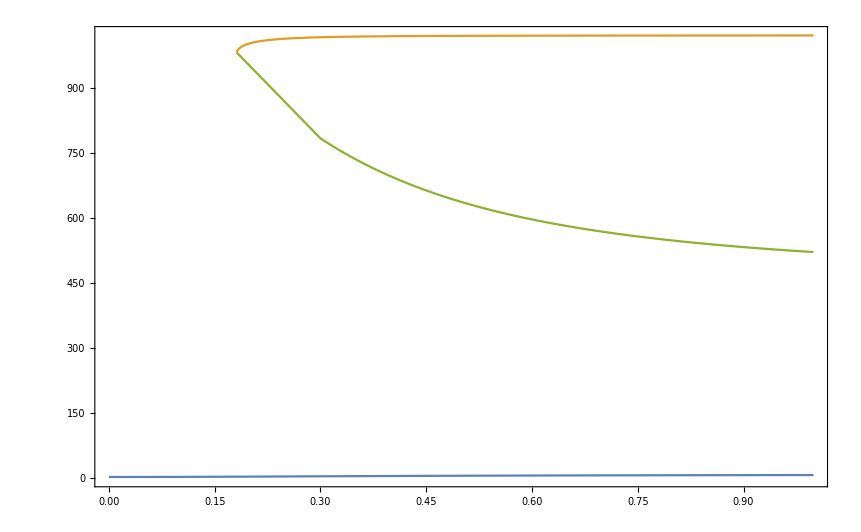

```mathematica
ListPlot[{Rds1[[1;; ]],Rds2[[1;; ]],Join[{Rds2[[1]]},Rds]},Joined->True,PlotRange->Full,Frame->True]
```

```mathematica
fixap={};ap=1;Rds1={};Rds2={};Rds={};Rds0={};Spo0Ap=0.3;
For[gr=0.05,gr<0.7,gr=gr+0.01,Spo0Apd:= (13+4 Spo0Ap-√13 √(13+8 *Spo0Ap))*125;sol=NSolve[{dSinId[Id,Rd]==0,dSinRd[Rd,Id,Ld]==0,SlrRtot[(SinRtot-SinISinR[Id,Rd]/2-Rd-SlrRSinR[Ld,Rd])]==SlrRSinR[Ld,Rd]+Ld,Ld>0,Rd>0,Id>0},{Ld,Rd,Id},Reals,WorkingPrecision->12];
fixap=Append[fixap,R/.solutions];
temp=Sort[Tap[SinRt[Id,Rd,Ld]]/.sol];
If[temp[[1]]<50,Rds1=Append[Rds1,{gr,temp[[1]]}]];
If[Last[temp]>50,Rds2=Append[Rds2,{gr,Last[temp]}]];
If[temp[[1]]<50 && Last[temp]>50 && temp[[-3]]>20,Rds=Append[Rds,{gr,temp[[-3]]}];Rds0=Append[Rds0,{gr,temp[[2]]}]];
]
```

ReplaceAll::reps: {solutions} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

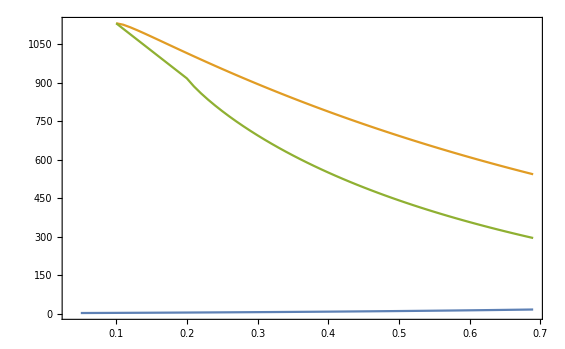

```mathematica
ListPlot[{Rds1,Rds2,Join[{Rds2[[1]]},Rds[[1;;]]]},Joined->True,PlotRange->Full,Frame->True]
```

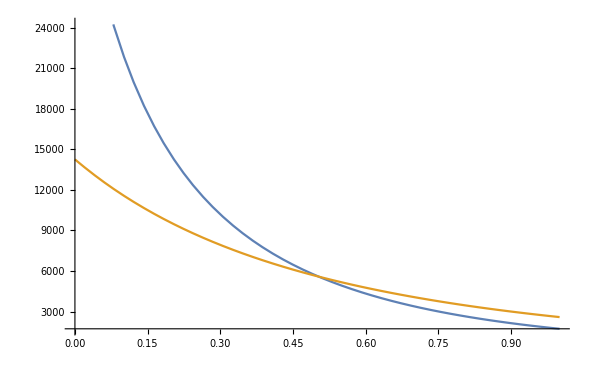

```mathematica
Plot[{SinRtot,SlrRtot[0]},{gr,0,1}]
```

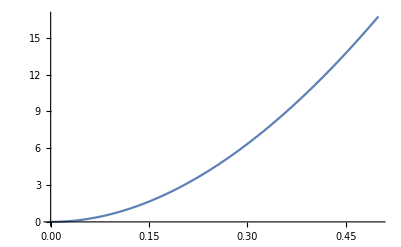

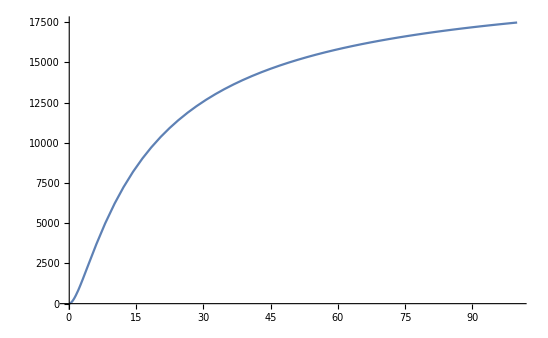

```mathematica
Spo0Apd:= (13+4 Spo0Ap-√13 √(13+8 *Spo0Ap))*125;Plot[{Spo0Apd},{Spo0Ap,0,0.5},PlotRange->Full]
```